Ref: https://www.youtube.com/watch?time_continue=26&v=U-L23G8lPQ8&feature=emb_logo

```mathematica
L = (M+m) x1'[t]^2+m h^2 θ1'[t]^2-2 m h x1'[t] θ1'[t] Cos[θ1[t]]-2 m g h Cos[θ1[t]]-k θ1[t]^2;
```

```mathematica
Qx1 = A Sin[ω t];
```

```mathematica
EulerLagrange[L_,q_,Q_]:=Block[{lhs,rhs},
lhs = D[D[L,q'[t]],t];
rhs = D[L,q[t]];
Solve[lhs-rhs==Q,q''[t]]
];
```

```mathematica
EulerLagrange[L,x1,Qx1]
```

{{x1''[t]→1/42 (5 Sin[t]-2 Sin[θ1[t]] θ1'[t]^2+2 Cos[θ1[t]] θ1''[t])}}

```mathematica
EulerLagrange[L,θ1,0]
```

{{θ1''[t]→0.5 (19.6 Sin[θ1[t]]-20. θ1[t]+2. Cos[θ1[t]] x1''[t])}}

```mathematica
g = 9.8;
m = 1;
M = 20;
k = 6;
h = 1;
l = 2;
A =5;
ω = 1;
```

```mathematica
solutions = NDSolveValue[
{
x1''[t]==(A Sin[t ω]-2 h m Sin[θ1[t]] θ1'[t]^2+2 h m Cos[θ1[t]] θ1''[t])/(2 (m+M)),
θ1''[t]==(g h m Sin[θ1[t]]-k θ1[t]+h m Cos[θ1[t]] x1''[t])/(h^2 m),
x1[0] == 0,x1'[0]==0,
θ1[0] == 0, θ1'[0]==0
},
{x1[t],θ1[t]},
{t,0,100}
];
```

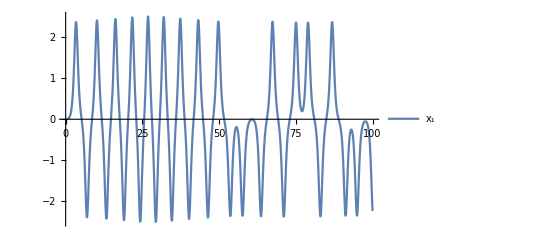

```mathematica
Plot[solutions[[2]],{t,0,100},PlotLegends->{"x_1","θ_1"},PlotRange->All,GridLines->{{},{-π/2,π/2}}]
```

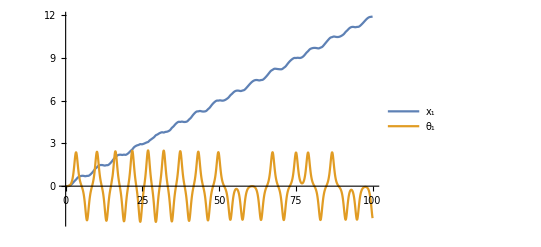

```mathematica
Plot[solutions,{t,0,100},PlotLegends->{"x_1","θ_1"},PlotRange->All]
```

### Sistema de referencia inercial

```mathematica
r1[x1_,θ1_]:={x1,0};
r2[x1_,θ1_]:={l+x1,0};
r3[x1_,θ1_]:={x1-h Sin[θ1],h Cos[θ1]};
r4[x1_,θ1_]:={l+x1-h Sin[θ1],h Cos[θ1]};

r1[tp_]:=Apply[r1,solutions/.t->tp];
r2[tp_]:=Apply[r2,solutions/.t->tp];
r3[tp_]:=Apply[r3,solutions/.t->tp];
r4[tp_]:=Apply[r4,solutions/.t->tp];
```

```mathematica
Manipulate[
Graphics[
{
Black,Line[{r1[t],r2[t]}],
Black,Line[{r3[t],r4[t]}],
Orange,Line[{r1[t],r3[t]}],
Orange,Line[{r2[t],r4[t]}],
Brown,Disk[r1[t],0.05],
Brown,Disk[r2[t],0.05],
Blue,Disk[r3[t],0.05],
Blue,Disk[r4[t],0.05]
},
PlotRange->{{-1,3},{-2,2}}
],
{t,0,100}
]
```

### Sistema de referencia dentro del edificio

```mathematica
r1e[x1_,θ1_]:={0,0};
r2e[x1_,θ1_]:={l,0};
r3e[x1_,θ1_]:={-h Sin[θ1],h Cos[θ1]};
r4e[x1_,θ1_]:={l-h Sin[θ1],h Cos[θ1]};

r1e[tp_]:=Apply[r1e,solutions/.t->tp];
r2e[tp_]:=Apply[r2e,solutions/.t->tp];
r3e[tp_]:=Apply[r3e,solutions/.t->tp];
r4e[tp_]:=Apply[r4e,solutions/.t->tp];
```

```mathematica
Manipulate[
Graphics[
{
Black,Line[{r1e[t],r2e[t]}],
Black,Line[{r3e[t],r4e[t]}],
Orange,Line[{r1e[t],r3e[t]}],
Orange,Line[{r2e[t],r4e[t]}],
Brown,Disk[r1e[t],0.05],
Brown,Disk[r2e[t],0.05],
Blue,Disk[r3e[t],0.05],
Blue,Disk[r4e[t],0.05]
},
PlotRange->{{-1,3},{-2,2}}
],
{t,0,100}
]
```

#### Para agregar el resorte al diagrama

Ojo: no es la solución con resorte, sólo un diagrama

```mathematica
DropSides[l_List]:=Take[l,{2,-2}];
AppendSides[l_List,left_,right_]:=Join[{left},l,{right}];
OddEven[l_List]:=Flatten[Partition[l,2,2,1,{}],{2}]; (* Source: https://mathematica.stackexchange.com/questions/21468/pretty-way-to-group-elements-at-odd-and-even-positions *)
Spring[{xi_,yi_},{xf_,yf_},div_,width_]:=Block[{xPoints,slope,xyPoints,d,odd,even,normalPointsOdd,normalPointsEven,zigzagPts,springCoords},
xPoints = Range[xi,xf-xi,(xf-xi)/div];
slope = (yf-yi)/(xf-xi);
xyPoints = Table[{x,slope(x-xi)+yi},{x,DropSides[xPoints]}];
{odd,even} = OddEven[xyPoints];
d = width*Normalize[{xf-xi,yf-yi}];
normalPointsOdd = Map[RotationMatrix[π/2].d+#&,odd];
normalPointsEven = Map[RotationMatrix[-π/2].d+#&,even];
zigzagPts = Riffle[normalPointsOdd,normalPointsEven];
springCoords = AppendSides[zigzagPts,{xi,yi},{xf,yf}];

Line[springCoords]
];
```

```mathematica
Manipulate[
Graphics[
{
Black,Line[{r1e[t],r2e[t]}],
Black,Line[{r3e[t],r4e[t]}],
Orange,Line[{r1e[t],r3e[t]}],
Orange,Line[{r2e[t],r4e[t]}],
Red,Spring[r1e[t],r4e[t],15,0.07],
Brown,Disk[r1e[t],0.05],
Brown,Disk[r2e[t],0.05],
Blue,Disk[r3e[t],0.05],
Blue,Disk[r4e[t],0.05]
},
PlotRange->{{-1,3},{-2,2}}
],
{t,0,100}
]
```